(√(1/a^3) ⅇ^(-r/a))/(√π)

(√(1/a^3) ⅇ^(-r/(2 a)) (2-r/a))/(4 √(2 π))

(√(1/a^3) ⅇ^(-r/(2 a)) r Cos[theta])/(4 a √(2 π))

-(√(1/a^3) ⅇ^(ⅈ phi-r/(2 a)) r Sin[theta])/(8 a √π)

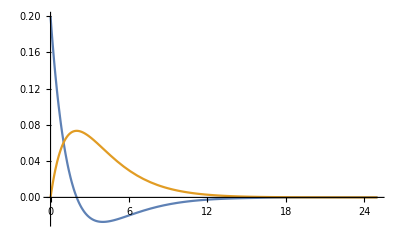

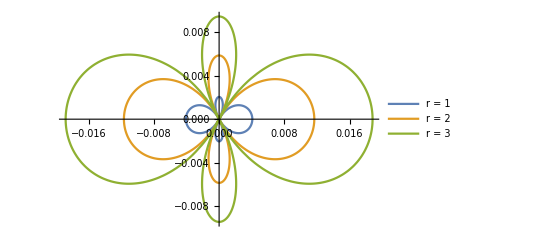

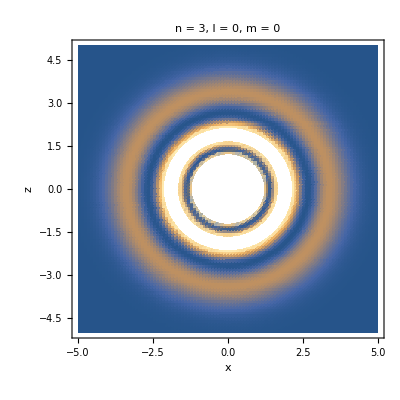
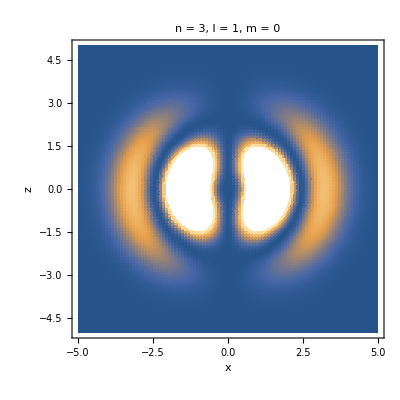
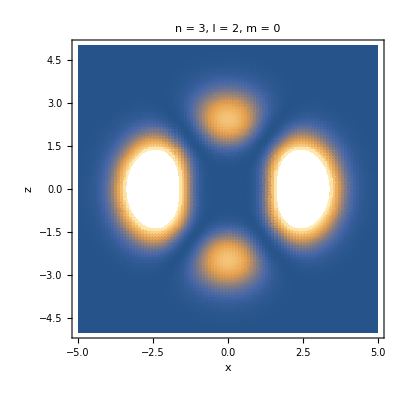

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

{1,0,0}

{2,0,0}

{2,1,0}

{2,1,1}

```mathematica
HydrogenWavefunction[{1,0,0},a,{r,theta,phi}] ;(*note that first its {n,l,m} then a is a variable ____ then r theta and phi are spherical coordinates*)
[{1,0,0},a,{r,theta,phi}] ;
(*so why are these 2 functions giving me different things? like i'm trying to call the same function*)
(*try again on the ground state*)
Clear[r,a,theta,phi];
ResourceFunction["HydrogenWavefunction"][{1,0,0},a,{r,θ,ϕ}];
Hwf = ResourceFunction["HydrogenWavefunction"];
Hwf[{1,0,0},a,{r,theta,phi}] (*ok now I have a shortcut for it*)
Hwf[{2,0,0},a,{r,theta,phi}] 
Hwf[{2,1,0},a,{r,theta,phi}] 
Hwf[{2,1,1},a,{r,theta,phi}] (*ok now I have some sense for how the quantum numbers, principal quantum number, angular and magnetic, how they fit into the wavefunction*)
(*now I will replicate some basic visualizations*)
With[{a=1},Plot[Evaluate[Re/@{Hwf[{2,0,0},a,{r,0,ϕ}],Hwf[{2,1,0},a,{r,0,ϕ}]}],{r,0,25},PlotRange->All]](*this is comparing radial dependence, like look out at the wavefunction value based on the wavelength given a=0*)
With[{a=1},PolarPlot[Evaluate[Table[Re@Hwf[{3,2,0},a,{r,θ,0}],{r,3}]],{θ,0,2π},{AspectRatio->1/GoldenRatio,PlotLegends->{"r = 1","r = 2","r = 3","r = 4"}}]](*now i'm curious what the axies mean, the previous one was angstroms and this one is also radius. Also this one is is getting basically different radius levels, at n=3, l=2 its evaluating r from 1 to 3, scaling upthis one radii*)
With[{a=1},Table[DensityPlot[Abs[Hwf[{3,l,0},a,{x^2+y^2,ArcTan[x,y],0}]]^2,{x,-5,5},{y,-5,5},{PlotPoints->100,PlotLabel->("n = 3, l = "<>IntegerString[l])<>", m = 0",FrameLabel->{"x","z"},RotateLabel->False}],{l,0,2}]](*i got the fancy plot labels from the documentation but all it's doing is plotting z as arctan makes it like a distace from nucleus right?*)
(*it's all squared so i know they're talking about electron probability density*)
ContourPlot3D[Evaluate[Abs[Hwf[{2,1,0},1,{Sqrt[x^2+y^2+z^2],If[Sqrt[x^2+y^2+z^2]==0,0,ArcCos[z/Sqrt[x^2+y^2+z^2]]],ArcTan[x,y]}]]^2],{x,-20,20},{y,-20,20},{z,-20,20},Contours->{0.0005,0.001,0.002},Mesh->None,PlotPoints->25](*maybe give this one some opacity, its the isosurface of constant probability density, how you usually represent orbitals*)
SphericalPlot3D[Evaluate[Abs[Hwf[{3,2,0},1,{6,θ,ϕ}]]^2],{θ,0,Pi},{ϕ,0,2 Pi},PlotRange->All](*ok but i actually don't know what this plot means physically, apparently its a topographic contor map of the spacial distribution of electron density. its most likley to be there, representingn a 2p orbital*)
ContourPlot3D[Evaluate[Abs[Hwf[{1,0,0},1,{Sqrt[x^2+y^2+z^2],If[Sqrt[x^2+y^2+z^2]==0,0,ArcCos[z/Sqrt[x^2+y^2+z^2]]],ArcTan[x,y]}]]^2],{x,-20,20},{y,-20,20},{z,-20,20},Contours->{0.0005,0.001,0.002},Mesh->None,PlotPoints->25]
ContourPlot3D[Evaluate[Abs[Hwf[{3,2,0},1,{Sqrt[x^2+y^2+z^2],If[Sqrt[x^2+y^2+z^2]==0,0,ArcCos[z/Sqrt[x^2+y^2+z^2]]],ArcTan[x,y]}]]^2],{x,-20,20},{y,-20,20},{z,-20,20},Contours->{0.0005,0.001,0.002},Mesh->None,PlotPoints->25]

(*n,l,m*)
{1,0,0}
{2,0,0}
{2,1,0}
{2,1,1}
```